```mathematica
b =1/2;
d = 3/2;
```

```mathematica
G=6.67 10^(-8);
R = 35336506;
AU = 1.5 10^13;
Td = 300 FT a^(-b);
Msun = 1.9891 10^33;
Me = 5.9742 10^27;
```

```mathematica
FT=1;
Clear[FT]
```

```mathematica
RB=G mc Me /(R Td)
```

(3.7589×10^10 √a mc)/FT

```mathematica
RH = (a AU) (mc Me /(3 mstar Msun))^(1/3)
```

1.50058×10^11 a (mc/mstar)^(1/3)

```mathematica
Solve[RB==RH, mc]
```

{{mc→0.},{mc→-(7.97621 a^(3/4) FT^(3/2))/(√mstar)},{mc→(7.97621 a^(3/4) FT^(3/2))/(√mstar)}}

```mathematica
Sigmad = 2200 FSigma a^(-d);
cd = (R Td)^(1/2);
Omega = (G mstar Msun/(a AU)^3)^(1/2);
Hd = cd/Omega;
rhod = Sigmad/(2 Hd)
```

(2.11824×10^-9 FSigma √(mstar/a^3))/(a^(3/2) √(FT/(√a)))

```mathematica
Hd
```

(5.193×10^11 √(FT/(√a)))/(√(mstar/a^3))

```mathematica
rhod = Simplify[rhod, {mstar>0, a>0, FT>0, d>0, b>0, b<2}]
```

(2.11824×10^-9 FSigma √(mstar/FT))/a^(11/4)

```mathematica
Matm = 4 Pi rhod RB^3/Me
```

(0.000236639 FSigma mc^3 √(mstar/FT))/(a^(5/4) FT^3)

```mathematica
FullSimplify[Matm]
```

(0.000236639 FSigma mc^3 √(mstar/FT))/(a^(5/4) FT^3)

```mathematica
Mth = mc/.Solve[RH == Hd, mc][[1]]
```

(41.4456 a^(5/2) FT √(FT/(√a)) √(mstar/a^3))/mstar

```mathematica
Simplify[Mth, {FT>0, a>0, mstar>0}]
```

(41.4456 a^(3/4) FT^(3/2))/(√mstar)

```mathematica
Matm2 = 4 Pi rhod RH^3/Me
```

(0.015055 a^(1/4) FSigma mc √(mstar/FT))/mstar

```mathematica
Simplify[Matm2, {mstar>0,a>0}]
```

(0.015055 a^(1/4) FSigma √(1/FT) mc)/(√mstar)

```mathematica
Matm2/mc
```

(0.015055 a^(1/4) FSigma √(mstar/FT))/mstar

```mathematica
D[Exp[rb/r] r^3, r]
```

3 ⅇ^(rb/r) r^2-ⅇ^(rb/r) r rb

```mathematica
Series[Exp[1/x], {x, 0.1, 5}]
```

22026.5-2.20265×10^6 (x-0.1)+1.32159×10^8 (x-0.1)^2-6.09399×10^9 (x-0.1)^3+2.37152×10^11 (x-0.1)^4-8.17182×10^12 (x-0.1)^5+O[x-0.1]^6

```mathematica
∫_rsw^rcb (1-A/r+A/rsw)^(1/(gamma1-1)) r^2ⅆr
```

ConditionalExpression[-(rsw ((-4+3 gamma1) (-A^2 (-2+gamma1)+2 (-1+gamma1)^2 rsw^2+A (rsw-gamma1 rsw))+A^2 (6-7 gamma1+2 gamma1^2) Hypergeometric2F1[1,1,4+1/(1-gamma1),(A+rsw)/A]))/(6 (-1+gamma1)^2 (-4+3 gamma1))+(rcb^3 (1+A (-1/rcb+1/rsw))^(1/(-1+gamma1)) ((-4+3 gamma1) (2 (-1+gamma1)^2 rcb^2 rsw^2+A (-1+gamma1) rcb rsw (4 (-1+gamma1) rcb+(3-4 gamma1) rsw)+A^2 (2 (-1+gamma1)^2 rcb^2+(-3+7 gamma1-4 gamma1^2) rcb rsw+(3-4 gamma1+2 gamma1^2) rsw^2))+A^2 (6-7 gamma1+2 gamma1^2) rsw^2 Hypergeometric2F1[1,1,4+1/(1-gamma1),(rcb (A+rsw))/(A rsw)]))/(6 (-1+gamma1)^2 (-4+3 gamma1) (A (rcb-rsw)+rcb rsw)^2),(rsw/(rcb-rsw)∉Reals||Re[rsw/(rcb-rsw)]<-1||(rsw≠0&&rcb rsw≠rsw^2&&Re[rsw/(rcb-rsw)]≥0))&&(rsw^2/((rcb-rsw) (A+rsw))∉Reals||Re[rsw^2/((rcb-rsw) (A+rsw))]>0||Re[rsw^2/((rcb-rsw) (A+rsw))]<-1)&&(rcb/(rcb-rsw)∉Reals||Re[rcb/(rcb-rsw)]>1||Re[rcb/(-rcb+rsw)]≥0)]

```mathematica
DSolve[{w''[z]+(2/z) w'[z] + w[z]==0, w[0]==1, w'[0]==0}, w[z], z]
```

{{w[z]→-(ⅈ ⅇ^(-ⅈ z) (-1+ⅇ^(2 ⅈ z)))/(2 z)}}

```mathematica
∫_0^rR r  Sin[r/ a]ⅆr
```

a (-rR Cos[rR/a]+a Sin[rR/a])

```mathematica
M=1.9 10^30;
R=7 10^9;
```

```mathematica
Pc=Pi/8 G M^2/R^4
```

3.93823×10^13

```mathematica
rhoc=Pi/4 M/R^3
```

4.3506

```mathematica
Cos[-Pi/2]
```

0

```mathematica
LegendreP[2, Cos[Pi/2]]
```

-1/2

```mathematica
Clear[a]
```

```mathematica
a=1
```

1

```mathematica
Sqrt[1.5 rho/P0]∫_0^a 1/(Sqrt[a^3/r^3-1])ⅆr
```

ConditionalExpression[(0.+0.528092 ⅈ) a √(rho/P0),Re[a]>0&&Im[a]==0]

```mathematica
N[Integrate[1/(Sqrt[a^3/r^3-1]), {r, 0, a}, Assumptions->a>0]]*Sqrt[1.5]
```

0.914681 a

```mathematica
1/(Sqrt[a^3/r^3-1])
```

1/(√(-1+a^3/r^3))

```mathematica
Gamma
```

```mathematica
∫1/(Sqrt[a^3/r^3-1])ⅆr
```

1/(√(-1+a^3/r^3) r^2)(r (a^2+a r+r^2)+1/(2 (-1+(-1)^(2/3)))(-1)^(2/3) a (a-r)^2 √(-((1+(-1)^(1/3)) r (a+(-1)^(1/3) r))/(a-r)^2) √((-a+(-1)^(2/3) r)/(-a+r)) ((3+ⅈ √3) EllipticE[ArcSin[(√(((3+ⅈ √3) r)/(-a+r)))/(√2)],(-ⅈ+√3)/(ⅈ+√3)]+(-1-ⅈ √3) EllipticF[ArcSin[(√(((3+ⅈ √3) r)/(-a+r)))/(√2)],(-ⅈ+√3)/(ⅈ+√3)]))

```mathematica
6 10^7 1.3 10^(-3)
```

78000.

```mathematica
6 10^7 (1.6/10-1+1.3 10^(-3))
```

-5.0322×10^7

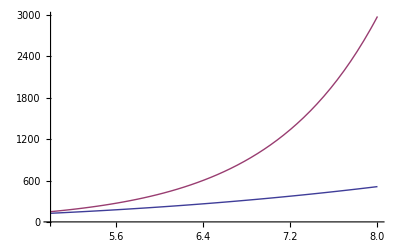

```mathematica
Plot[{x^3, Exp[x]}, {x, 5, 8}]
```

```mathematica
Exp[1.1]
```

3.00417

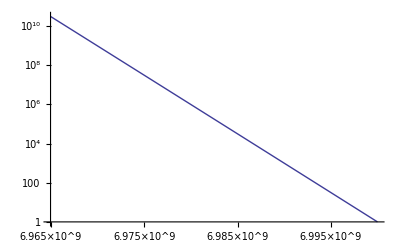

```mathematica
Rp= 7 10^9;
Hp=R 100 Rp^2/(G (300 Me));
LogLogPlot[Exp[-r/Hp] Exp[Rp/Hp] , {r, 0.995Rp,Rp}]
```

```mathematica
4 10^3 0.005
```

20.

```mathematica
Plot[Exp[Rp^2/(Hp r)] Exp[-Rp/(Hp )]  * r^3, {r, 0.9999Rp,Rp}]
```

-Graphics-

```mathematica
Rp^2/(Hp 0.9 Rp)
```

5369.86

```mathematica
Rp^2/(Hp Rp)
```

4832.87

```mathematica
Hp/6/10^8
```

0.00241402

```mathematica
Exp[100.]
```

2.68812×10^43

```mathematica
Exp[-20.]
```

2.06115×10^-9

```mathematica
D[Exp[-x] x^3, x]
```

3 ⅇ^-x x^2-ⅇ^-x x^3

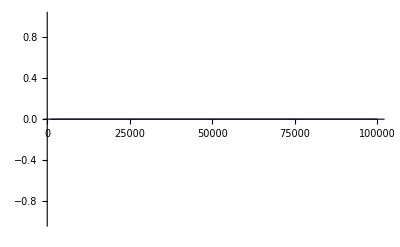

```mathematica
Plot[Exp[-x]  x^3, {x, 1000, 100000}]
```

```mathematica
Rp/Hp
```

4832.87

```mathematica
rho = 5;
alpha = 7 10^10/(a AU);
sigma = 7 * a^(-3/2);
Omega = (G Msun/(a AU)^3)^(1/2);
```

```mathematica
tiso = (rho a AU/sigma)^(1/2) alpha^(1/2)/Omega/(365 24 3600)
```

(35762.2 √(1/a) √(a^(5/2)))/(√(1/a^3))

```mathematica
(sigma a AU/(rho alpha))^(1/2)/10^5
```

1189.24 a^(1/4)

```mathematica
1./234
```

0.0042735

```mathematica
alpha
```

0.00466667/a

```mathematica
0.5^0.25
```

0.840896

```mathematica
rho
```

5